# Mathematica 实战演练 之 函数定义 & 递归 陈可鉴 2024-03-02

## Intro

关于此次 workshop

QQ 群、讲义

QQ 群号：892799351

#### -Graphics-

关于我

## 语法快速教学

赋值

像其他很多编程语言一样，Mathematica 也有同样的赋值语法。

```mathematica
x=1
{a,b}={3,4}
```

1

{3,4}

```mathematica
{a,b}={b,a}
```

{4,3}

注意：既然 = 用来表示赋值了，那么判断相等就只能用 == 了，切勿混淆

## 延迟赋值

对比两种情况

```mathematica
r=RandomReal[](*注意：在赋值的瞬间先计算了 RHS，每次调用结果相同*)
```

0.702418

```mathematica
{r,r,r}
```

{0.702418,0.702418,0.702418}

```mathematica
r:=RandomReal[] (*赋值时并未计算 RHS，而是留到调用时再计算，所以每次结果不同*)
```

```mathematica
{r,r,r}
```

{0.366193,0.243089,0.0302098}

## 清除赋值

注意观察符号的染色：黑色代表有值，蓝色代表无值

可以用 Unset ( =. ) 来取消赋值

```mathematica
x=.
```

Clear 和 ClearAll 能清除符号的各种属性和值

```mathematica
Clear[a,b,r]
```

## 作用域（局部变量）

很多时候我们并不希望用全局变量（比如在定义函数时，我们希望一些变量属于函数体内部，不要暴露在外）。而清除-再赋值的方法也太笨拙了，因此我们需要「作用域」来实现局部变量。
参见：guide/ScopingConstructs

常用的作用域函数：With, Block, Module, DynamicModule。它们彼此间有一些微妙的不同，同学们可以自行阅读它们的帮助文档。

```mathematica
a=1
Block[{a},Print@a](*在 Block 内部，a 的全局定义被屏蔽了，取而代之的是局部定义*)
```

1

a

```mathematica
a=.
```

规则 & 替换

Mathematica 有别于一般编程语言的很重要的一点是，Mathematica 是符号式的，这为公式推导提供了很大的便利。然而，「赋值」会破坏符号的未定义形式，在后续计算时强制代入，诸多不便。

规则（Rule）表示一种变换法则（这与数学里的「代换」「变换」的思想类似）
基于规则替换的编程是一种强大灵活的范式。它允许我们对表达式做细致的操控。

## ReplaceAll ( /. )

例子：
（这里的 /. 全称是 ReplaceAll）

```mathematica
list={1,2,3,4,5,4,3,2,1};
```

```mathematica
list/.{3->0} (*把其中的 3 替换为 0*)
```

{1,2,0,4,5,4,0,2,1}

```mathematica
list/.{{3->a},{3->b}} (*执行两个不同的规则*)
```

{{1,2,a,4,5,4,a,2,1},{1,2,b,4,5,4,b,2,1}}

规则替换 可以替换表达式的任意部分，包括其「头部」（Head）

```mathematica
f[x]/.f->Sin
```

Sin[x]

## 延迟规则 RuleDelayed

与延迟赋值类似，延迟规则也并不先计算规则的 RHS（右手边），而是等到应用该规则时再替换

```mathematica
{r,r,r}/.r->RandomReal[]
{r,r,r}/.r:>RandomReal[]
```

{0.665977,0.665977,0.665977}

{0.279411,0.763991,0.553365}

到目前为止，规则替换似乎只能将特定的 LHS（左手边）进行替换。我们即将看到，结合「模式」，规则替换可以发挥出巨大威力。

模式 Pattern

模式是理解 Mathematica 语法的关键，也是后续定义复杂且灵活的函数所必须掌握的知识。
内置文档有个详细的教程可以参看：tutorial/Patterns

要理解什么是模式，我们先来看一个例子：

在这个例子中，每一个匹配 f[x_] 的表达式都被转化为了 x^2。x_ 就是一个模式，可以匹配任意一个表达式。实际上，_ (Blank) 代表一个任意表达式，前面的 x 是给这个模式一个简称，让它可以后续被调用。

```mathematica
f[a]+f[b+c]+d+Sin@e/.f[x_]:>x^2
```

a^2+(b+c)^2+d+Sin[e]

MatchQ 可以用来检查一个表达式是否与某个模式匹配：
可以看到，只有匹配的表达式才会应用该规则替换

```mathematica
MatchQ[f[a],f[x_]]
MatchQ[f[b+c],f[x_]]
MatchQ[d,f[x_]]
MatchQ[Sin[e],f[x_]]
```

True

True

False

False

我自定义了一个函数，用来高亮表达式中与模式相匹配的部分

```mathematica
(*这个函数大家不用学习，只是用来辅助看清模式的*)
ClearAll@highlightPattern
SetAttributes[highlightPattern,HoldFirst]
highlightPattern[expr_,patt_]:=ReplaceAll[HoldForm@expr,x:patt:>Highlighted@x]
```

```mathematica
highlightPattern[f[a]+f[b+c]+d+Sin@e,f[x_]]
```

f[a]+f[b+c]+d+Sin[e]

## 各种各样的模式

Mathematica 中的模式非常灵活，有很多种类，还可以进一步组合。
具体可以在帮助文档 guide/Patterns 和 tutorial/PatternsAndTransformationRules 里看到

### 限制模式

例如：可以用 PatternTest ( ? ) 或者 Condition ( /; ) 来限制模式：

```mathematica
list={1,2,3,4,5,4,3,2,1};
```

```mathematica
list/.{_?OddQ->0}(*_?OddQ 是一个模式，_ 先匹配到一个任意表达式，然后用 OddQ 来测试它，只有给出 True 的才匹配*)
```

{0,2,0,4,0,4,0,2,0}

```mathematica
highlightPattern[Evaluate@list,_?OddQ]
```

{1,2,3,4,5,4,3,2,1}

```mathematica
list/.{x_/;x>3->0}
(*/;x>3 要求 x 对应的表达式 >3 时才匹配*)
```

{1,2,3,0,0,0,3,2,1}

如果我想把 list 里的所有数都变成 0 ，该怎么做？

```mathematica
list/.{x_->0}
```

0

上面这样写是不行的，因为整个 list 也是「单个表达式」，优先匹配并替换了。

```mathematica
highlightPattern[Evaluate@list,_]
```

{1,2,3,4,5,4,3,2,1}

这时就要限制模式，不让它匹配到最外层的整个列表，而是匹配里面的数字

```mathematica
list/.{x_?NumericQ->0}
list/.{x_Integer->0}
```

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0}

_Integer 这种写法是限制该表达式的 「头部」 Head 必须为 Integer

```mathematica
{Head@3,Head@3.5,Head@{1,2,3},Head@f[3]}
```

{Integer,Real,List,f}

### 模式序列

__ （双下划线）：一个或多个表达式序列
___ （三下划线）：零个或多个表达式序列

```mathematica
list/.{left___,a_,b_,right___}/;a+b==5:>{left,xxx,right}
(*注意，只替换了第一个匹配的，后面还有一个表达式序列 3,2 也匹配，但并没有替换*)
```

{1,xxx,4,5,4,3,2,1}

## 重复替换 //.

//. （ReplaceRepeated）会不停地应用规则替换，直到表达式不再改变（不动点）

例子：应用 Log 的展开法则，把表达式完全展开

```mathematica
rules={Log[x_ y_]:>Log[x]+Log[y],Log[x_^k_]:>k Log[x]};
Log[√(a (b c^d)^e)]//.rules
```

1/2 (Log[a]+e (Log[b]+d Log[c]))

可以查看每一步展开的结果

```mathematica
FixedPointList[ReplaceAll@rules,Log[Sqrt[a(b c^d)^e]]]
```

{Log[√(a (b c^d)^e)],1/2 Log[a (b c^d)^e],1/2 (Log[a]+Log[(b c^d)^e]),1/2 (Log[a]+e Log[b c^d]),1/2 (Log[a]+e (Log[b]+Log[c^d])),1/2 (Log[a]+e (Log[b]+d Log[c])),1/2 (Log[a]+e (Log[b]+d Log[c]))}

函数式编程

参见：guide/FunctionalProgramming

Mathematica 的一大编程范式就是函数式编程，也就是说，由「函数套函数套函数」来完成运算

## 纯函数 / 匿名函数

我们先来看看最「简单纯粹」的函数应该如何定义：

```mathematica
func1=Function[x,x^2]
```

Function[x,x^2]

```mathematica
func1[3]
func1[{3,4,5}]
```

9

{9,16,25}

可以用 # (Slot 插符) 作为语法糖，快捷地定义纯函数

```mathematica
(#^2&)@3
```

9

多个变量的纯函数

```mathematica
func2=Function[{x,y},x+y];
func2[a,b]
```

a+b

同样可以用 # 来写，#1 代表所接受的第一个参数

```mathematica
(#1+#2)&[a,b]
```

a+b

## 定义函数

通过模式来定义函数，其实和模式匹配的 ReplaceAll 很类似

```mathematica
func3[{x_,y_},a_]:=x^2+y^2-a
func3[{3,4},5]
```

20

可以为函数设定不同的模式，从而轻松实现对多种输入的灵活处理：

```mathematica
func3[{x_,y_},{a_,b_}]:=x^2+y^2-a-b
```

可以将一种输入模式归约到另一种

```mathematica
func3[l1_List][l2_]:=func3[l1,l2]
```

```mathematica
func3[{3,4}][{5,6}]
```

14

对于不匹配任何模式的输入，函数原样返回，并不报错！

```mathematica
func3[3,4,5]
```

func3[3,4,5]

清除函数定义，用 Clear 或 ClearAll

```mathematica
ClearAll[func3]
```

例子：递归定义阶乘函数

```mathematica
ClearAll@fact
```

```mathematica
fact[n_Integer/;n>0]:=n fact[n-1]
fact[0]=1;
```

```mathematica
fact[-10]
```

fact[-10]

过程式编程

除了函数式编程，Mathematica 也支持过程式编程的范式。（不过本质上还是函数式的）

## 顺序

用分号 ; 把各个语句连接起来，或者直接换行。分号有抑制输出的功能。

2 Cos[x] Sin[x]

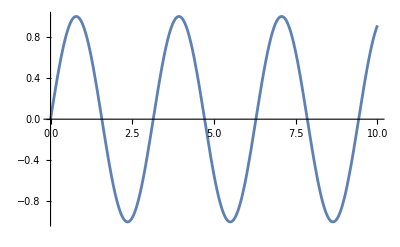

```mathematica
expr1=Sin[x]^2;
expr2=D[expr1,x];
%//Print
Plot[expr2,{x,0,10}]
```

## 分支

Mathematica 里的 If 也只是一个函数。根据判断条件的真假，执行并返回不同的分支。
存在一种情况，既不是 True 也不是 False，这时如果提供了第三个分支（第四个参数），则返回该分支。

```mathematica
If[x>5,"若为 True 返回这个","若为 False 返回这个"]
```

If[x>5,若为 True 返回这个,若为 False 返回这个]

## 循环

Do 循环的语法与 Table 完全类似，只不过 Do 是执行其循环体内的语句，但并不创建一个列表把返回值储存下来。

```mathematica
Do[Echo@i,{i,1,5,2}]
```

1

3

5

While 循环非常简单，与其他语言类似。

```mathematica
i=1;
While[i<10,Echo@i;i*=2]
```

1

2

4

8

Mathematica 中的 For 循环语法与 C 类似，但强烈不推荐使用！！！在几乎任何情况下都应该避免使用 For 而是用 Do 和 While 来代替。

在循环中，可以通过 Break、Continue、Return 等函数（注意是函数而非「语句」「关键字」）来实现跳出循环等控制流程。

## 斐波那契数

为什么选取这一个例子？

数学定义

```mathematica
-Graphics-
-Graphics-,-Graphics-
```

我故意选取 fib[0]==0, fib[1]==1 的定义：为了演示更多功能

为了演示，我基本上都用「函数定义」的语法，把各种实现都定义为 fib 函数（这也符合 Mathematica 的函数式风格）。

「最后只给出第 n 个数」 vs 「给出长为 n 的数列」：
前者节省内存，后者在反复计算时更快。作为演示，我们这里实现前者。

迭代：自底而上

## 循环

Do 循环（练习）

```mathematica
ClearAll@fib
fib[n_]:=Block[{a,b},
{a,b}={0,1};
Do[{a,b}={b,a+b},n];
a
]
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

```mathematica
fib[10000]
```

While 循环

```mathematica
ClearAll@fib
fib[n_]:=Block[{a,b,i=n},
{a,b}={0,1};
While[i-->0,{a,b}={b,a+b}];
a
]
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

## 规则替换

```mathematica
ClearAll@fib
fib[n_]:={0,1,0}//.{a_,b_,i_/;i<n}:>{b,a+b,i+1}//First
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

## Nest 函数嵌套

```mathematica
fib[n_]:=Nest[{Last@#,Total@#}&,{0,1},n][[1]]
fib[n_]:=Nest[Comap@{Last,Total},{0,1},n][[1]]
```

```mathematica
NestList[{Last@#,Total@#}&,{0,1},10][[;;,1]]
```

{0,1,1,2,3,5,8,13,21,34,55}

递归：自顶而下

## 分支判断

Mathematica 中分支语句有多种：If 、Which、Switch，功能比较相似。除此之外，Piecewise 作为数学上的分段函数也可以起到分支的功能。

If 、Which、Switch 分支

这几种写法等价：

```mathematica
ClearAll@fib
fib[n_]:=If[n==0,0,If[n==1,1,fib[n-1]+fib[n-2]]]
fib[n_]:=Which[n==0,0,n==1,1,True,fib[n-1]+fib[n-2]]
fib[n_]:=Switch[n,0,0,1,1,_,fib[n-1]+fib[n-2]]
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

Piecewise 分段函数（练习）

```mathematica
ClearAll@fib
fib[n_]:=Piecewise[{{n, n==1||n==0}, {fib[n-1]+fib[n-2], True}}]
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

## 函数定义（基于模式匹配的多态）

```mathematica
ClearAll@fib
fib[n_]:=fib[n-1]+fib[n-2]
fib[0]=0;
fib[1]=1;
(*fib[n:0|1]:=n;*)
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

```mathematica
fib[30]//Timing
```

{0.905749,832040}

## 纯函数

```mathematica
fib=If[#==0||#==1,#,fib[#-1]+fib[#-2]]&;
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

你可能会发现上面的纯函数不够「纯」，因为调用了 fib 这个名称

```mathematica
fib=If[#==0||#==1,#,#0[#-1]+#0[#-2]]&;
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

## 规则替换

```mathematica
rule=n_/;n>1:>(n-1/.rule)+(n-2/.rule);
Range[0,10]/.rule
```

{0,1,1,2,3,5,8,13,21,34,55}

## 鬼画符

挑战：看懂这行代码（留作习题）
注：这段代码对于 0 不正确

```mathematica
1/. _:>#0[#-1]+#0[#-2]/;#>2&/@Range@10
```

{1,1,2,3,5,8,13,21,34,55}

递归的优化

## 速度测试

之前的递归版本，算 n=10 还行，n=30 就要 1s 了！

```mathematica
ClearAll@fib
fib[n_]:=fib[n-1]+fib[n-2]
fib[0]=0;
fib[1]=1;

fib[10]//Timing
fib[30]//Timing
```

{0.000121,55}

{1.17895,832040}

实际上，这种递归的复杂度是 O(ⅇ^n) 的！
原因在于大量的重复计算。

## 记忆化递归（缓存）

空间换时间

```mathematica
ClearAll@fib
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
fib[0]=0;
fib[1]=1;
fib[1000]//Timing
```

{0.004367,43466557686937456435688527675040625802564660517371780402481729089536555417949051890403879840079255169295922593080322634775209689623239873322471161642996440906533187938298969649928516003704476137795166849228875}

```mathematica
fib[1001]//Timing
```

{0.000011,70330367711422815821835254877183549770181269836358732742604905087154537118196933579742249494562611733487750449241765991088186363265450223647106012053374121273867339111198139373125598767690091902245245323403501}

## 尾递归

实际上相当于迭代

```mathematica
ClearAll[fib]
fib[n_,a_:0,b_:1]:=fib[n-1,b,a+b]
fib[0,a_,b_]:=a
```

```mathematica
fib[10000]
```

$IterationLimit::itlim: 超过 4096 的迭代极限.

TerminatedEvaluation[IterationLimit]

为了绕过迭代限制，用 Block 局部修改变量的值

```mathematica
Block[{$IterationLimit=∞},fib[10000]]//Short
```

33644764876431783266621612005107«2025»976171121233066073310059947366875

数学优化

「数学优化是降维打击」

## 线性递推

```mathematica
RecurrenceTable[{a[n]==a[n-1]+a[n-2],a[0]==0,a[1]==1},a, {n,0,10}]
```

{0,1,1,2,3,5,8,13,21,34,55}

```mathematica
LinearRecurrence[{1,1},{1,1},10]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
RSolve[{a[n]==a[n-1]+a[n-2],a[0]==0,a[1]==1},a[n],n]
```

{{a[n]→Fibonacci[n]}}

## 通项公式

基于线性递推方程，可以推导出斐波那契数列的通项公式：

```mathematica
Round[GoldenRatio^n/(√5)]//TraditionalForm
```

Round[ϕ^n/(√5)]

```mathematica
ClearAll@fib
fib[n_]:=Round[GoldenRatio^n/(√5)]
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

```mathematica
fib[10^6]==Fibonacci[10^6]
```

True

## 矩阵快速幂

注意到线性递推关系可以写成矩阵形式

```mathematica
({{1, 1}, {1, 0}}).{b,a}
```

{a+b,b}

因此，矩阵反复作用于初值向量，就是迭代的过程

```mathematica
NestList[({{1, 1}, {1, 0}}).#&,{1,0},10]
```

{{1,0},{1,1},{2,1},{3,2},{5,3},{8,5},{13,8},{21,13},{34,21},{55,34},{89,55}}

我们可以直接从矩阵的分量读出斐波那契数

```mathematica
MatrixPower[({{1, 1}, {1, 0}}),10]
```

{{89,55},{55,34}}

```mathematica
ClearAll@fib
fib[n_]:=MatrixPower[({{1, 1}, {1, 0}}),n][[1,2]]
fib/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

矩阵幂乘 A^n 的时间复杂度是多少？

O(log(n))

MatrixPower 甚至还可以解析计算！

```mathematica
MatrixPower[({{0, 1}, {1, 1}}),n]//Simplify//MatrixForm
```

((2^(-1-n) ((1-√5)^n (1+√5)+(-1+√5) (1+√5)^n))/(√5) | (2^-n (-(1-√5)^n+(1+√5)^n))/(√5)
(-(1/2 (1-√5))^n+(1/2 (1+√5))^n)/(√5) | (2^(-1-2 n) ((2-2 √5)^n (-1+√5)+2^n (1+√5)^(1+n)))/(√5))

```mathematica
fib[n]//Simplify
```

(2^-n (-(1-√5)^n+(1+√5)^n))/(√5)

## 练习：「折半」公式

利用矩阵形式可以推导出如下关系：
-Graphics-
可以看到，这样每次递归直接把 n 归约为原来的 1/2。因此，递归可以从 O(n) 优化到 O(log(n)) ，甚至不需要缓存。
请运用各种方法，实现这一算法。

## 最重要的：内置函数

```mathematica
Fibonacci/@Range[0,10]
```

{0,1,1,2,3,5,8,13,21,34,55}

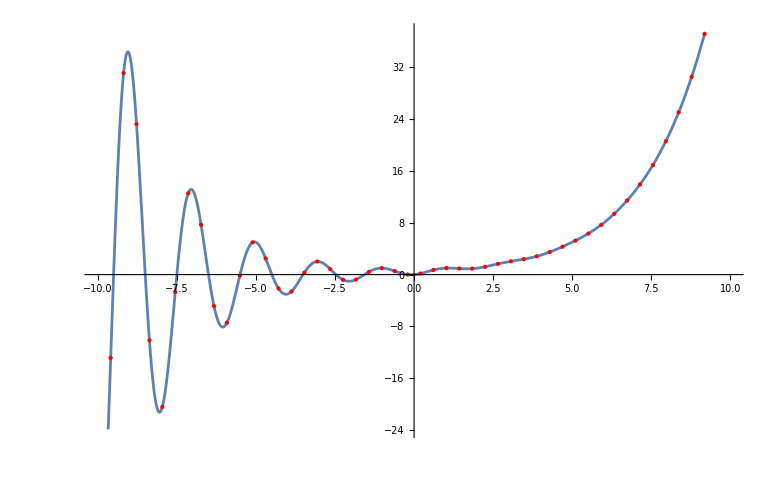

```mathematica
Plot[Fibonacci[n],{n,-10,10},Mesh->Full,MeshStyle->Red]
```

## 习题参考

```mathematica
ClearAll[fib]
fib[n_?OddQ]:=fib[(n+1)/2]^2+fib[(n-1)/2]^2
fib[n_?EvenQ]:=fib[n/2](fib[n/2]+2fib[n/2-1])
fib[0]=0;
fib[1]=1;
```

```mathematica
fib[1000]==Fibonacci@1000
```

True

写出更好的函数

## 清除定义

## 鲁棒性：对模式的限制

## 多态与归约

## 函数属性

## 高阶函数 / 算子

习题：排序算法

推荐写冒泡排序 & 快速排序，自己查资料喔

```mathematica
Needs@"GeneralUtilities`"
```

```mathematica
Clear@GeneralUtilities`Performance`PackagePrivate`$TimingCaches
```

```mathematica
??BenchmarkPlot
```

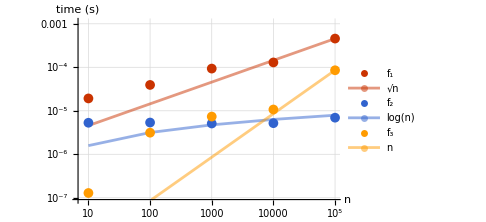

```mathematica
BenchmarkPlot[{fib,Round[GoldenRatio^#/(√5)]&,Fibonacci},#&,10^Range[5],TimeConstraint->20,MaxIterations->1024,"IncludeFits"->True]
```

```mathematica
GU`PD@BenchmarkPlot
```

comments:
自底而上：节省内存，容易记忆化。但不够灵活
自顶而下：直观符合定义，可以很灵活。但堆栈可能爆内存。

## Take Home Message

初始化单元

```mathematica
(*SetOptions[EvaluationNotebook[],CellContext->CellGroup]*)
```